```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210718_product_diversity"];
```

```mathematica
ccm=Import["../data/ccm_manipulated_347418.csv"];
csp=Import["../data/csp_manipulated_205496_rev1.csv"];
pltcm=Import["../data/pltcm_manipulated_59604_rev1.csv"];
cgl=Import["../data/cgl_manipulated_27147_rev1.csv"];
```

```mathematica
(*MemberQ[pltcm[[All,{4,3}]],cgl[[405,{3,4}]]]
ContainsAll[pltcm[[All,{4,3}]],cgl[[All,{3,4}]]]
Length@Intersection[cspdata[[All,{16,17}]],pltcmdata[[All,{21,22}]]]
Length@Intersection[cspdata[[All,{16,17}]],ccmdata[[All,{7,6}]]]*)
```

```mathematica
histrow[width_,thick_,data_]:=GraphicsRow[{Histogram[width,PlotRange->Full,Frame->True,FrameLabel->{"Max. Width Differences in Sequences","Counts"},ImageSize->Medium],Histogram[thick,PlotRange->Full,Frame->True,FrameLabel->{"Max. Thickness Differences in Sequences","Counts"},ImageSize->Medium],{MinMax@data[[All,9]],MinMax@data[[All,10]]}}];
```

```mathematica
histogram[data_,name_]:=GraphicsRow[{name,Histogram[data[[All,9]],PlotRange->Full,Frame->True,FrameLabel->{"Width Values","Counts"},ImageSize->Medium],Histogram[data[[All,10]],PlotRange->Full,Frame->True,FrameLabel->{"Thickness Values","Counts"},ImageSize->Medium]}];
```

```mathematica
data=ccm;
seqgroupswidth=Values@GroupBy[Thread[{data[[All,9]],data[[All,2]]}],Last->First];
seqgroupsthick=Values@GroupBy[Thread[{data[[All,10]],data[[All,2]]}],Last->First];row1=histrow[Table[Abs@((MinMax@seqgroupswidth[[i]])[[1]]-(MinMax@seqgroupswidth[[i]])[[2]]),{i,Length@seqgroupswidth}],Table[Abs@((MinMax@seqgroupsthick[[i]])[[1]]-(MinMax@seqgroupsthick[[i]])[[2]]),{i,Length@seqgroupsthick}],ccm];
```

```mathematica
data=csp;
seqgroupswidth=Values@GroupBy[Thread[{data[[All,9]],data[[All,2]]}],Last->First];
seqgroupsthick=Values@GroupBy[Thread[{data[[All,10]],data[[All,2]]}],Last->First];row2=histrow[Table[Abs@((MinMax@seqgroupswidth[[i]])[[1]]-(MinMax@seqgroupswidth[[i]])[[2]]),{i,Length@seqgroupswidth}],Table[Abs@((MinMax@seqgroupsthick[[i]])[[1]]-(MinMax@seqgroupsthick[[i]])[[2]]),{i,Length@seqgroupsthick}],csp];
```

```mathematica
data=pltcm;
seqgroupswidth=Values@GroupBy[Thread[{data[[All,9]],data[[All,2]]}],Last->First];
seqgroupsthick=Values@GroupBy[Thread[{data[[All,10]],data[[All,2]]}],Last->First];row3=histrow[Table[Abs@((MinMax@seqgroupswidth[[i]])[[1]]-(MinMax@seqgroupswidth[[i]])[[2]]),{i,Length@seqgroupswidth}],Table[Abs@((MinMax@seqgroupsthick[[i]])[[1]]-(MinMax@seqgroupsthick[[i]])[[2]]),{i,Length@seqgroupsthick}],pltcm];
```

```mathematica
data=cgl;
seqgroupswidth=Values@GroupBy[Thread[{data[[All,9]],data[[All,2]]}],Last->First];
seqgroupsthick=Values@GroupBy[Thread[{data[[All,10]],data[[All,2]]}],Last->First];row4=histrow[Table[Abs@((MinMax@seqgroupswidth[[i]])[[1]]-(MinMax@seqgroupswidth[[i]])[[2]]),{i,Length@seqgroupswidth}],Table[Abs@((MinMax@seqgroupsthick[[i]])[[1]]-(MinMax@seqgroupsthick[[i]])[[2]]),{i,Length@seqgroupsthick}],cgl];
```

```mathematica
GraphicsColumn[{row1,row2,row3,row4}]
```

-Graphics-

```mathematica
GraphicsColumn[{histogram[ccm,"CCM"],histogram[csp,"CSP"],histogram[pltcm,"PLTCM"],histogram[cgl,"CGL"]}]
```

-Graphics-

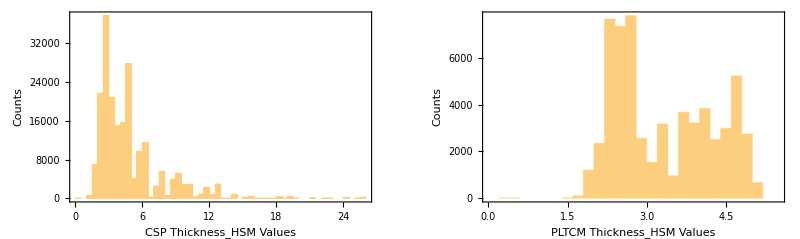

```mathematica
GraphicsRow[{Histogram[csp[[All,15]],PlotRange->Full,Frame->True,FrameLabel->{"CSP Thickness_HSM Values","Counts"},ImageSize->Medium],Histogram[pltcm[[All,17]],PlotRange->{{0,5.5},All},Frame->True,FrameLabel->{"PLTCM Thickness_HSM Values","Counts"},ImageSize->Medium]}]
```

```mathematica
GraphicsColumn[{GraphicsRow[{Histogram[csp[[All,10]],PlotRange->{{50,80},All},Frame->True,FrameLabel->{"CSP Thickness Values","Counts"},ImageSize->Medium],Histogram[pltcm[[All,10]],PlotRange->{{0,5.5},All},Frame->True,FrameLabel->{"PLTCM Thickness Values","Counts"},ImageSize->Medium],Histogram[cgl[[All,10]],PlotRange->{{0,5.5},All},Frame->True,FrameLabel->{"CGL Thickness Values","Counts"},ImageSize->Medium]}],GraphicsRow[{Histogram[csp[[All,9]],PlotRange->{{500,2000},All},Frame->True,FrameLabel->{"CSP Width Values","Counts"},ImageSize->Medium],Histogram[pltcm[[All,9]],PlotRange->{{500,2000},All},Frame->True,FrameLabel->{"PLTCM Width Values","Counts"},ImageSize->Medium],Histogram[cgl[[All,9]],PlotRange->{{500,2000},All},Frame->True,FrameLabel->{"CGL Width Values","Counts"},ImageSize->Medium]}]}]
```

-Graphics-

PLTCM features

```mathematica
GraphicsColumn[{GraphicsRow[{Histogram[pltcm[[All,9]],PlotRange->{{500,2000},All},Frame->True,FrameLabel->{"Width_input Values","Counts"},ImageSize->Medium],Histogram[pltcm[[All,16]],PlotRange->{{500,2000},All},Frame->True,FrameLabel->{"Width_target Values","Counts"},ImageSize->Medium],Histogram[pltcm[[All,20]],PlotRange->{{500,2000},All},Frame->True,FrameLabel->{"Width Values","Counts"},ImageSize->Medium]}],GraphicsRow[{Histogram[pltcm[[All,10]],PlotRange->{{0,5.5},All},Frame->True,FrameLabel->{"Thickness_input Values","Counts"},ImageSize->Medium],Histogram[pltcm[[All,15]],PlotRange->{{0,5.5},All},Frame->True,FrameLabel->{"Thickness_target Values","Counts"},ImageSize->Medium],Histogram[pltcm[[All,18]],PlotRange->{{0,5.5},All},Frame->True,FrameLabel->{"Thickness Values","Counts"},ImageSize->Medium]}]}]
```

-Graphics-

CGL features

```mathematica
GraphicsColumn[{GraphicsRow[{Histogram[cgl[[All,9]],PlotRange->{{500,2000},All},Frame->True,FrameLabel->{"Width Values as PLTCM Output","Counts"},ImageSize->Medium],Histogram[cgl[[All,5]],PlotRange->{{500,2000},All},Frame->True,FrameLabel->{"Width Values in CGL Data Set","Counts"},ImageSize->Medium]}],GraphicsRow[{Histogram[cgl[[All,10]],PlotRange->{{0,3.5},All},Frame->True,FrameLabel->{"Thickness Values as PLTCM Output","Counts"},ImageSize->Medium],Histogram[cgl[[All,6]],PlotRange->{{0,3.5},All},Frame->True,FrameLabel->{"Thickness Values in CGL Data Set","Counts"},ImageSize->Medium]}]}]
```

-Graphics-

```mathematica
GraphicsColumn[{GraphicsRow[{Histogram[pltcm[[All,9]],PlotRange->{{500,2000},All},Frame->True,FrameLabel->{"PLTCM Width_input Values","Counts"},ImageSize->Medium],Histogram[pltcm[[All,25]],PlotRange->{{0,1600},All},Frame->True,FrameLabel->{"PLTCM Length_input Values","Counts"},ImageSize->Medium],Histogram[pltcm[[All,10]],PlotRange->{{0,5.5},All},Frame->True,FrameLabel->{"PLTCM Thickness_input Values","Counts"},ImageSize->Medium]}],GraphicsRow[{Histogram[cgl[[All,9]],PlotRange->{{500,2000},All},Frame->True,FrameLabel->{"CGL Width Values (PLTCM Outcomes)","Counts"},ImageSize->Medium],Histogram[cgl[[All,8]],{10^2},PlotRange->{{0,6000},All},Frame->True,FrameLabel->{"CGL Length Values","Counts"},ImageSize->Medium],Histogram[cgl[[All,10]],PlotRange->{{0,5.5},All},Frame->True,FrameLabel->{"CGL Thickness Values (PLTCM Outcomes)","Counts"},ImageSize->Medium]}]}]
```

-Graphics-